```mathematica
SetDirectory["/Users/Jenna/jennaproject/mma"]
```

/Users/Jenna/jennaproject/mma

```mathematica
kvals=Import["~/jennaproject/data/kvals.txt","List"][[1;;420]];
plin=Import["~/jennaproject/data/plin.txt","List"][[1;;420]];
b1b2=Import["~/jennaproject/data/b1b2.txt","List"][[1;;420]];
b2b2=Import["~/jennaproject/data/b2b2.txt","List"][[1;;420]];
b1br=Import["~/jennaproject/data/b1br.txt","List"][[1;;420]];
b2br=Import["~/jennaproject/data/b2br.txt","List"][[1;;420]];
brbr=Import["~/jennaproject/data/brbr.txt","List"][[1;;420]];
Dimensions[brbr]
```

{420}

```mathematica
a=ListLogLogPlot[{kvals,plin}ᵀ,Joined->True,PlotStyle->{Thick,Red}];
b=ListLogLogPlot[{kvals,Abs[b1b2]}ᵀ,Joined->True,PlotStyle->{Thick,Red}];
c=ListLogLogPlot[{kvals,Abs[b2b2]}ᵀ,Joined->True,PlotStyle->{Thick,Blue}];
d=ListLogLogPlot[{kvals,Abs[b1br]}ᵀ,Joined->True,PlotStyle->{Thick,Green}];
e=ListLogLogPlot[{kvals,Abs[b2br]}ᵀ,Joined->True,PlotStyle->{Thick,Orange}];
f=ListLogLogPlot[{kvals,Abs[brbr]}ᵀ,Joined->True,PlotStyle->{Thick,Purple}];
g=ListLogLogPlot[{kvals,(plin+b1b2+b2b2+b1br+b2br+brbr)}ᵀ,Joined->True,PlotStyle->{Thick,Black}];
```

```mathematica
Show[a,b,c,d,e,f,g];
```

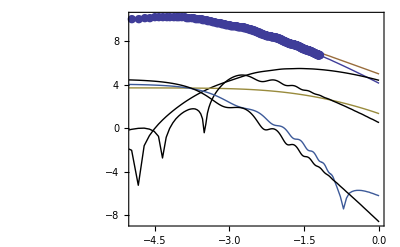

```mathematica
a=ListLogLogPlot[{{kvals,plin}ᵀ,{kvals,Abs[b1b2]}ᵀ,{kvals,Abs[b2b2]}ᵀ,{kvals,Abs[b1br]}ᵀ,{kvals,Abs[b2br]}ᵀ,{kvals,Abs[brbr]}ᵀ,{kvals,(plin+b1b2+b2b2+b1br+b2br+brbr)}ᵀ},Joined->True,PlotStyle->{Thick,Black},PlotMarkers-> {Automatic,Small},PlotLegend->{Style["Linear",18],Style["b1b2",18],Style["b2b2",18],Style["b1br",18],Style["b2br",18],Style["brbr",18],Style["All",18]},LegendShadow->None,LegendPosition->{0.9,-0.3},Joined->True,PlotStyle->Thick,BaseStyle->{FontSize->22},Frame->True, FrameLabel->{"k (h Mpc^-1)","Galaxy Power Spectrum P_g(k)/b_1^2 (Mpc^3)"},RotateLabel->True,PlotLabel->"Power spectrum breakdown by higher order terms"]
```